## Wobbling Frequencies for 163Lu using the Parity-Partner procedure

```mathematica
ClearAll["Global`*"]
```

```mathematica
path[filename_]:=StringTemplate["/Users/basavyr/Documents/Work/PhD/163Lu-New-TSD4-Formalism/Code/Update-July-2022/plots/``"][filename];
export[filename_,obj_]:=Export[path[filename],Show[obj],ImageResolution->1200];
texStyle={FontFamily->"Latin Modern Roman",FontSize->22};
```

## Analytic formulas

```mathematica
B1[I_,j_,A1_,A2_,A3_,V_,γ_]:=-(((2I-1)(A3-A1)+2j*A1)*((2I-1)(A2-A1)+2j*A1)+8A2*A3*I*j+((2j-1)(A3-A1)+2I*A1+V(2j-1)/(j(j+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]))*((2j-1)(A2-A1)+2I*A1+V(2j-1)/(j(j+1))2 √3 Sin[γ*π/180]));
C1[I_,j_,A1_,A2_,A3_,V_,γ_]:=(((2I-1)(A3-A1)+2j*A1)*((2j-1)(A3-A1)+2I*A1+V*(2j-1)/(j(j+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]))-4I*j*A3^2)*(((2I-1)(A2-A1)+2j*A1)*((2j-1)(A2-A1)+2I*A1+V*(2j-1)/(j(j+1))2 √3 Sin[γ*π/180])-4I*j*A2^2);
Omega1[I_,j_,A1_,A2_,A3_,V_,γ_]:=√(1/2(-B1[I,j,A1,A2,A3,V,γ]-(B1[I,j,A1,A2,A3,V,γ]^2-4C1[I,j,A1,A2,A3,V,γ])^(1/2)));
Omega2[I_,j_,A1_,A2_,A3_,V_,γ_]:=√(1/2(-B1[I,j,A1,A2,A3,V,γ]+(B1[I,j,A1,A2,A3,V,γ]^2-4C1[I,j,A1,A2,A3,V,γ])^(1/2)));
```

## Parameter set 𝒫_fit={A1,A2,A3,V,γ}

```mathematica
j1=13/2;A1=1/(2*72);A2=1/(2*15);A3=1/(2*7);V=2.1;gm=22;shiftTSD2=0.3;shiftTSD4=0.6;
```

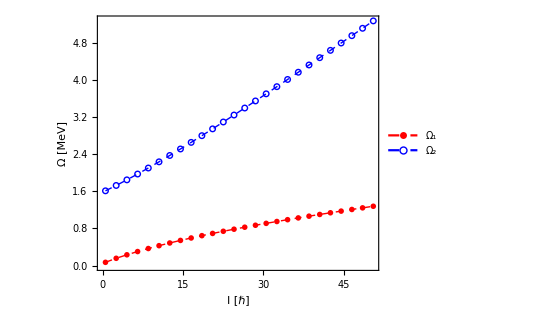

```mathematica
omegaplot=ListPlot[{Table[{x,Omega1[x,j1,A1,A2,A3,V,gm]},{x,0.5,51,2}],Table[{x,Omega2[x,j1,A1,A2,A3,V,gm]},{x,0.5,51,2}]},AspectRatio->0.8,Frame->True,ImageSize->400,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"I [ℏ]","Ω [MeV]"},LabelStyle->texStyle,PlotStyle->{{Red,Dashed,Thick},{Blue,Dashed,Thick}},Joined->True,PlotMarkers->{{"●",Scaled[0.04]},{"○",Scaled[0.05]}},PlotLegends->Placed[{"Ω_1","Ω_2"},{0.2,0.8}]];
Show[omegaplot]
export["wobblingFrequency.pdf",omegaplot];
```